```mathematica
v[{s_,i_,r_}]:={-γ s i + λ r,γ s i - i,i - λ r}

n=1
c=0.056
d=22
l=1/180
λ=c d
γ =l d 

G=RotationMatrix[{{1,1,1},{0,0,1}}];(* rotates the normal of Λ to the s-axis *)
```

1

0.056

22

1/180

1.232

11/90

```mathematica
pSu=AffineTransform[{G, {0,0,-n/Sqrt[3]}}];
R=Transpose[G];
uSp=AffineTransform[{R,-R.{0,0,-n/Sqrt[3]}}];
Area[Triangle[{{n,0,0},{0,n,0},{0,0,n}}]]
Area[Triangle[{pSu[{n,0,0}],pSu[{0,n,0}],pSu[{0,0,n}]}]]
uSp[pSu[{s,i,r}]]//Simplify
pSu[uSp[{p,q,z}]]//Simplify

pSu[v[uSp[{p,q,0}]]]//FullSimplify
G.v[uSp[{p,q,0}]]//FullSimplify
```

(√3)/2

(√3)/2

{s,i,r}

{p,q,z}

{0.425392+0.0203704 p^2+p (-0.917819-0.0814815 q)+(-1.28384+0.0203704 q) q,-0.291447-0.0203704 p^2+p (0.0518446+0.0814815 q)+(-1.31418-0.0203704 q) q,-0.57735-1.75443×10^-17 p-1.75443×10^-17 q}

{0.425392+0.0203704 p^2+p (-0.917819-0.0814815 q)+(-1.28384+0.0203704 q) q,-0.291447-0.0203704 p^2+p (0.0518446+0.0814815 q)+(-1.31418-0.0203704 q) q,-1.75443×10^-17 p-1.75443×10^-17 q}

```mathematica
Q=Orthogonalize[{Normalize[{-1,1,0}],Normalize[{-1,-1,2}],Normalize[{1,1,1}]}]
```

{{-1/(√2),1/(√2),0},{-1/(√6),-1/(√6),√(2/3)},{1/(√3),1/(√3),1/(√3)}}

```mathematica
ParametricPlot[{p,q},
{p,q}∈Triangle[{{1/12 (6+2 √3) n,1/12 (-6+2 √3) n},{1/12 (-6+2 √3) n,1/12 (6+2 √3) n},{-n/(√3),-n/(√3) }}],
BoundaryStyle->Directive[Gray, Thick],
Axes->True,
FrameLabel->(Style[#,Black,24,Bold]&/@{"p", "q"}),
RotateLabel->False,
FrameStyle->Directive[Black,Thickness@0.006],
PerformanceGoal->"Quality"
]

ParametricPlot3D[uSp[{p,q,0}],
{p,q}∈Triangle[{{1/12 (6+2 √3) n,1/12 (-6+2 √3) n},{1/12 (-6+2 √3) n,1/12 (6+2 √3) n},{-n/(√3),-n/(√3) }}], 
BoundaryStyle->Directive[Gray, Thick],
PerformanceGoal->"Quality",
AxesLabel->(Style[#,Black,24,Bold]&/@{"s","i","r"}),
BoxStyle->Directive[Black,Thickness@0.006],
TicksStyle->Directive[Bold,Black]]
```

-Graphics-

-Graphics3D-

```mathematica
Solve[1/γ+λ x+x==1,x]
a=(-1+γ)/(γ (1+λ))
```

{{x→-3.21766}}

-3.21766

```mathematica
eqPoint={1/γ,λ a,a}
Total[eqPoint]//Simplify
τ=0.05;
f[{a_,b_}]:=eqPoint+a/Sqrt[2]{-1,1,0}+b/Sqrt[2]{-1,0,1}
points=f/@RandomReal[{-1,1},{75,2}];
StreamPlot3D[v[{s, i, r}],{s,0,n},{i,0,n},{r,0,n},StreamMarkers->"Arrow",
StreamPoints->points,
PerformanceGoal->"Quality",
AxesLabel->(Style[#,Black,24,Bold]&/@{"s","i","r"}),
BoxStyle->Directive[Black,Thickness@0.006],
TicksStyle->Directive[Bold,Black],
ImageSize->Large]
```

{90/11,-3.96416,-3.21766}

1.

-Graphics3D-

```mathematica
data=Table[v[{s, i, r}],{s,0,n},{i,0,n},{r,0,n}];
ListSliceVectorPlot3D[data, 
ImplicitRegion[s+i+r==n, {s, i, r}], 
DataRange->{{0,n},{0,n},{0,n}},
BoundaryStyle->Directive[Gray, Thick],
VectorSizes->0.3,
PerformanceGoal->"Quality",
AxesLabel->(Style[#,Black,24,Bold]&/@{"s","i","r"}),
BoxStyle->Directive[Black,Thickness@0.006],
TicksStyle->Directive[Bold,Black],
VectorColorFunction->"SolarColors",
ImageSize->Large
(*PlotLabel->StringForm["λ=``, γ=``",λ,γ]*)
]
```

-Graphics3D-

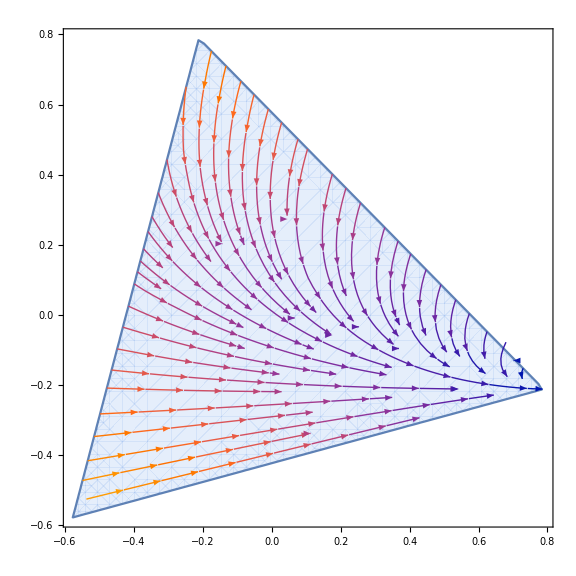

```mathematica
StreamPlot[Drop[G.v[uSp[{p,q,0}]],-1],
{p,q}∈Triangle[{{1/12 (6+2 √3) n,1/12 (-6+2 √3) n},{1/12 (-6+2 √3) n,1/12 (6+2 √3) n},{-n/(√3),-n/(√3) }}],
VectorSizes->0.5,
Axes->{False,False},
PerformanceGoal->"Quality",
VectorColorFunction->"SolarColors",
ImageSize->Large
]
```